# Learning = Representation + Evaluation + Optimization a few useful things to know about machine learning

#### Image, Video, Audio, Taste/Smell https://ai.googleblog.com/2019/10/learning-to-smell-using-deep-learning.html Text, Intuition, Action

## Deep learning work flow -- using CNN as an example MNIST, CIFAR-10, CIFAR-100, https://datarepository.wolframcloud.com/category/Machine-Learning

ImageNet

```mathematica
resource = ResourceObject["MNIST"];
trainingData = ResourceData[resource, "TrainingData"];
testData = ResourceData[resource, "TestData"];
```

```mathematica
Length[trainingData]
```

60000

```mathematica
RandomSample[trainingData, 5]
```

{-Graphics-→8,-Graphics-→2,-Graphics-→0,-Graphics-→7,-Graphics-→1}

```mathematica
trainingData[[1,1]]
ImageData[trainingData[[1,1]]]
```

-Graphics-

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.8,0.376471,0.00784314,0.376471,0.803922,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.811765,0.0666667,0.0117647,0.0117647,0.0117647,0.0705882,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.788235,0.109804,0.00784314,0.0117647,0.0627451,0.0862745,0.0117647,0.776471,0.976471,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.960784,0.764706,0.121569,0.0117647,0.00784314,0.0117647,0.207843,0.670588,0.0117647,0.00784314,0.521569,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.360784,0.0117647,0.0117647,0.0117647,0.00784314,0.0117647,0.0117647,0.623529,0.258824,0.00784314,0.345098,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.8,0.0666667,0.00784314,0.00784314,0.254902,0.552941,0.00784314,0.105882,0.815686,0.690196,0.,0.341176,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,0.811765,0.0666667,0.0117647,0.0117647,0.298039,0.952941,0.705882,0.52549,0.917647,1.,1.,0.00784314,0.0470588,0.803922,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,0.85098,0.352941,0.00784314,0.0862745,0.184314,0.670588,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.352941,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,0.972549,0.301961,0.0117647,0.0588235,0.721569,0.92549,0.890196,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.235294,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,0.776471,0.0117647,0.0117647,0.752941,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.235294,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,0.223529,0.00784314,0.254902,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.00784314,0.231373,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.701961,0.0352941,0.0117647,0.560784,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.419608,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.0980392,0.901961,1.,1.,1.,1.,1.,1.,1.,1.,0.972549,0.470588,0.00784314,0.270588,0.952941,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.12549,1.,1.,1.,1.,1.,1.,1.,1.,0.972549,0.486275,0.0117647,0.117647,0.721569,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.431373,1.,1.,1.,1.,1.,1.,1.,0.811765,0.352941,0.0117647,0.321569,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.662745,0.00784314,0.117647,1.,1.,1.,1.,1.,1.,0.552941,0.0666667,0.00784314,0.364706,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.0235294,0.427451,0.811765,0.886275,0.666667,0.301961,0.117647,0.00784314,0.12549,0.345098,0.780392,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.0117647,0.0117647,0.101961,0.156863,0.0117647,0.0117647,0.0117647,0.231373,0.490196,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.890196,0.219608,0.0117647,0.0117647,0.00784314,0.0117647,0.0117647,0.0862745,0.431373,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,0.901961,0.498039,0.0117647,0.00784314,0.0117647,0.447059,0.854902,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
X2=nl(A1X1+B1)
X3=nl(A2X2+B2)
```

```mathematica
A = NetChain[
  {ConvolutionLayer[20, 5], Ramp, PoolingLayer[2, 2], 
   ConvolutionLayer[50, 5], Ramp, PoolingLayer[2, 2], FlattenLayer[], 
   500, Ramp, 10, SoftmaxLayer[]},
  "Output" -> NetDecoder[{"Class", Range[0, 9]}],
  "Input" -> NetEncoder[{"Image", {28, 28}, "Grayscale"}]
  ]
```

NetChain[<>]

```mathematica
lenet = NetTrain[lenet, trainingData, 
   ValidationSet -> testData, 
   (*TargetDevice->{"GPU",All},*)
   MaxTrainingRounds -> 3];
```

```mathematica
Information[lenet]
```

Net Information

```mathematica
https://reference.wolfram.com/language/ref/TrainingProgressReporting.html
```

```mathematica
imgs = Keys @ RandomSample[testData, 5];
Thread[imgs -> lenet[imgs]]
```

{-Graphics-→5,-Graphics-→6,-Graphics-→5,-Graphics-→5,-Graphics-→8}

## https://resources.wolframcloud.com/NeuralNetRepository

```mathematica
unet=NetModel["U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a Polyacrylamide Substrate Data"]
netevaluate[img_, device_: "CPU"] :=
 Block[
  {net = NetModel[
     "U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a \
Polyacrylamide Substrate Data"],
   dims = ImageDimensions[img], pads, mask},
  pads = Map[{Floor[#], Ceiling[#]} &, Mod[4 - dims, 16]/2];
  mask = NetReplacePart[
     net,
     {"Input" -> 
       NetEncoder[{"Image", Ceiling[dims - 4, 16] + 188, 
         ColorSpace -> "Grayscale"}],
      "Output" -> NetDecoder[{"Class", Range[2], "InputDepth" -> 3}]}][
    ImagePad[ColorConvert[img, "Grayscale"], pads + 92, 
     Padding -> "Reversed"],
    TargetDevice -> device
    ];
  Take[mask, {1, -1} Reverse[pads[[2]] + 1], {1, -1} (pads[[1]] + 1)]
  ]
```

NetGraph[<>]

```mathematica
mask = netevaluate[sf];
```

```mathematica
{sf,Colorize[mask],HighlightImage[sf, Image[mask - 1, "Bit"]]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Examples

#### Style Transfer

```mathematica
cezanne=NetModel["CycleGAN Photo-to-Cezanne Translation"];
vangogh=NetModel["CycleGAN Photo-to-Van Gogh Translation"];
monet=NetModel["CycleGAN Photo-to-Monet Translation"];
```

```mathematica
TableForm[{{cezanne[sf],vangogh[sf],monet[sf]}}]
```

-Graphics- | -Graphics- | -Graphics-

#### GAN (https://reference.wolfram.com/language/ref/NetGANOperator.html)

#### Reinforcement learining

DeviceObject[…]

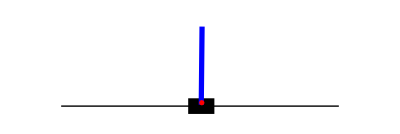

```mathematica
env = DeviceOpen["SimulatedCartPole"]
DeviceExecute[env, "Render"]
```

```mathematica
policyNet = 
 NetInitialize@
  NetChain[{64, Tanh, 2, SoftmaxLayer[]}, "Input" -> 4, 
   "Output" -> NetDecoder[{"Class", {Left, Right}}]]
```

NetChain[<>]

```mathematica
reinforceLoss = 
 NetGraph[{CrossEntropyLossLayer["Index"], 
   ThreadingLayer[#1*#2 &]}, {NetPort["DiscountedReward"] -> 
    2, {NetPort["Input"], NetPort["Action"]} -> 1 -> 2}, 
  "Action" -> NetEncoder[{"Class", {Left, Right}}]]
```

NetGraph[<>]

```mathematica
discountedSum[rewards_List, gamma_] := 
  Dot[rewards, gamma ^ Range[0, Length[rewards] - 1]];
applyDiscount[rewards_List, gamma_] :=
 	
 Table[discountedSum[Drop[rewards, i - 1], gamma], {i, Length@rewards}]
	
CollectEpisodes[env_, policyNet_, totalNumberSteps_Integer, 
   maxStepsPerEp_Integer, discountFactor_] := Module[
   {
    action, actions, epActions, observedState, observedStates, 
    epObservedStates, reward, rewards, discountedRewards, 
    epDiscountedRewards, ended, currentSteps
    },
   
   epActions = {}; epObservedStates = {}; epDiscountedRewards = {};
   
   currentSteps = 0;
   
   (* episode loop *)
   While[
    currentSteps < totalNumberSteps
    ,
    observedStates = {}; rewards = {}; actions = {};
    
    (* start each new episode with a fresh environment *)
    
    observedState = DeviceExecute[env, "Reset"]["ObservedState"];
             
    (* step loop *)
    Do[
     AppendTo[observedStates, observedState];
     
     action = policyNet[observedState];
     
     {observedState, reward, ended} = 
      Lookup[DeviceExecute[env, "Step", action],
       {"ObservedState", "Reward", "Ended"}];
     
     AppendTo[rewards, reward];
     AppendTo[actions, action];
     
     If[ended, Break[]];
     ,
     Min[maxStepsPerEp, totalNumberSteps - currentSteps]
     ];
    
    discountedRewards = applyDiscount[rewards, discountFactor];
    
    epActions = Join[epActions, actions];
    	epObservedStates = Join[epObservedStates, observedStates];
    	epDiscountedRewards = 
     Join[epDiscountedRewards, discountedRewards];
    
    currentSteps += Length @ actions;
    	];
   
   	<|"Action" -> epActions, "ObservedState" -> epObservedStates, 
    "DiscountedReward" -> epDiscountedRewards|>
   ];
```

```mathematica
reinforceSampler[env_, net_, batchSize_] := Block[{data},
   	data = CollectEpisodes[
     		env, net[#, "RandomSample"] &,
     		batchSize, 50, 0.99
     	];
   	data["Input"] = data["ObservedState"];
   	data
   ];
```

```mathematica
reinforceSampler[env, policyNet, 2]
```

<|Action→{Right,Right},ObservedState→{{-0.0229855,-0.0449351,0.0261371,-0.0283234},{-0.0238842,0.149802,0.0255706,-0.312647}},DiscountedReward→{1.99,1.},Input→{{-0.0229855,-0.0449351,0.0261371,-0.0283234},{-0.0238842,0.149802,0.0255706,-0.312647}}|>

```mathematica
results = 
 NetTrain[policyNet, reinforceSampler[env, #Net, #BatchSize] &, All,
  LossFunction -> reinforceLoss, Method -> "RMSProp",
  BatchSize -> 1024, MaxTrainingRounds -> 50, 
  TrainingProgressMeasurements -> <|
    "Measurement" -> NetPort["DiscountedReward"], 
    "Aggregation" -> "Mean", "Key" -> "Reward"|>
  ]
trained = results["TrainedNet"];
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:50  rounds:50  time:32s  examples/s:1637
data | ,,  training examples:1024  processed examples:51200  skipped examples:0
method | ,,  RMSPropoptimizer  batch size1024CPU
round | ,,  loss:1.04×10^1  Reward:2.16×10^1
 | 
 | ]

```mathematica
DeviceExecute[env, "Reset"];
ListAnimate[
  Table[(DeviceExecute[env, "Step", 
     DeviceExecute[env, trained[DeviceRead[env]["ObservedState"]]]]; 
    DeviceExecute[env, "Render"]), 50]]
```

```mathematica
DeviceExecute[env, "Reset"];
ListAnimate[
  Table[(DeviceExecute[env, "Step", 
     DeviceExecute[env, "RandomAction"]]; 
    DeviceExecute[env, "Render"]), 50]]
```

#### https://community.wolfram.com/groups/-/m/t/1127985

## Frontiers

#### Geometric deep learning https://www.youtube.com/user/keenancrane probabilistic deep learning https://www.manning.com/books/probabilistic-deep-learning deep learning + physics